# 第1章 Mathematica的基本量

## 1.1 数值

### 1.Mathematica 中建立了四种基本的数的类型.

Mathematica 中数的类型
"Integer" | "1234" | "任意长度的精确整数"
"Rational" | "1234/222" | "整数除整数的最简形式"
"Real" | "123.4" | "近似实数,具有任意指定的精度"
"Complex" | "12+34I" | "复数"
 
（1）	对整数或有理数进行四则运算，结果会给出精确值.
（2）	对实数进行四则运算，结果是具有指定精度的实数, 不指定时，给出6位有效数字，
（3）	如果使用复数， 应当注意当输入一个数如 123+0I.时， Mathematica 把它作为实数处理， 如果需要做复数运算，例如复数开根号，需要输入123+0.0I

```mathematica
Head[123+0I]
Head[123+0.0I]
```

Integer

Complex

### 2.不同形式之间的转换

(1)"N[x,n]" | "将转换为位精度的近似实数"
"Rationalize[x]" | "  给出的有理数近似值"
"Rationalize[x,dx]" | "给出的误差不超过的有理数近似值"

```mathematica
N[5/7,30]  
Rationalize[N[Pi]] 
 Rationalize[N[Pi],10^(-5)]
```

0.714285714285714285714285714286

3.14159

355/113

```mathematica
NumberQ[π]
```

False

```mathematica
Rationalize[N[Pi],0]
```

245850922/78256779

(2)
"IntegrPart[x]" | " X 的整数部分"
"FractionalPart[x]" | " X 的小数部分"
"Round[x]" | "最接近x的整数 "
"Floor[x]" | " 小于等于x 的最大整数"
"Ceiling[x]" | " 大于等于 X 的最小整数"

IntegrPart[x]和 FractionalPart[x]可以看作是提取小数点左边和右边的数字.Round[ x ]表示4舍5入的结果.Floor[x]和 Ceiling[x]常出现在计算一个具有非整数间隔的数列中有多少元素的事项中

```mathematica
Round[-3.1]
Round[2.6]
```

-3

3

```mathematica
Floor[-3.1]
Floor[2.6]
```

-4

2

(3)
"x+yI" | "复数" | "Conjugate[z]" | "z的共轭"
"Re[z]" | "实部" | "Im[z]" | "虚部"
"Abs[z]" | "模长" | "Arg[z]" | "辐角"

```mathematica
Re[12+3.0I]
```

12.

(4)角度与弧度转换

```mathematica
Sin[60 Degree]
```

(√3)/2

```mathematica
Sin[60 °]
```

Sin[60]

```mathematica
Sin[Pi/3]
```

(√3)/2

(5)不同进制的转换
" b^^digits" | "b进制的数digits转为10进制"
"BaseForm[x,b]" | "10进制数 x 转为 b 进制数"
"IntegerDigits[n,b]" | "整数n在b进制下的数字列表，b缺省表示10进制"
"IntegerDigits[n,b,l]" | "左边补零使列表长度为l"
"RealDigits[n,b]" | "给出实数x在b进制下的数字列表及小数点左边位数，b缺省表示10进制 "

```mathematica
2^^100101
```

37

```mathematica
BaseForm[37, 2]
```

100101_2

```mathematica
16^^ff1faa00
```

4280265216

```mathematica
BaseForm[ N[Sqrt[2],30], 8]
```

1.324047463177167462204262766115467_8

```mathematica
RealDigits[123.456789012345678901234567]
```

{{1,2,3,4,5,6,7,8,9,0,1,2,3,4,5,6,7,8,9,0,1,2,3,4,5,6,7},3}

```mathematica
FromDigits[%]
```

123456789012345678901234567/1000000000000000000000000

```mathematica
IntegerDigits[56, 2,8]
```

{0,0,1,1,1,0,0,0}

### 3. 常用数值函数

(1) 
"Random[ ]" | "生成[0,1]中的一个伪随机数"
"Random[ Real,xmax ]
Random[ Real,{xmin ,xmax },l ]" | "生成[0,xmax]或[xmin,xmax] 中的一个伪随机数,
参数 l 是生成随机数的数字位数"
"Random[Complex]
Random[Complex,{zmin,zmax} ]" | "生成单位方形区域或zmin,zmax为对角顶点的矩形
区域中的一个伪随机数"
"Random[ Integer]" | "具有相同概率 的 0 或 1"
"Random[ Integer, {imin , imax} ]" | "生成 [xmin,xmax] 中的一个伪随机数"
"SeedRandom[ ]
SeedRandom[ s]" | "将伪随机数生成器的起点重设为时钟时刻或整数s "

```mathematica
Table[Random[ ],{5}]
```

{0.240591,0.140657,0.0854972,0.856496,0.35773}

```mathematica
Random[Real,{ 0,10}]
```

4.123424257

```mathematica
Table[Random[ Integer, {100, 200} ] ,{8} ]
```

{134,143,186,159,173,168,154,175}

用法：(1)使用伪随机数的一个常见方法是进行数值假设检验.例如， 如果用户相信两个符号表达式在数学上是相等的.可以通过给符号参数插上"典型"数值的值.然后比较数值结果来进行检验。

(2)其它常见用法包括模拟随机过程， 概率空间的采样.
Mathematica 生成的伪随机数总是在指定范围上的均匀分布.

由 Random[ ]得到的序列在多数意义下并不是"真正随机的"， 尽管实际上它们应当是"足够随机的".如果用户想确定总是得到相同的伪随机数序列， 可以使用 SeedRandom[]给伪随机数一个起点.

```mathematica
SeedRandom[100];Table[Random[],{5}]
```

{0.185898,0.242848,0.20331,0.0515874,0.440317}

```mathematica
Table[Random[],{5}]
```

{0.239615,0.817663,0.23069,0.986929,0.262161}

```mathematica
SeedRandom[100];Table[Random[],{5}]
```

{0.185898,0.242848,0.20331,0.0515874,0.440317}

每调用一次 Random,伪随机数生成器的内部状态就被改变， 这意味着在辅助运算中调用 Random,将会影响主运算中 Random 返回的数.要避免这个问题， 可以在辅助运算之前保存 $StateRandom 的值，以后再恢复它.

```mathematica
Block[{$RandomState} ,{Random[ ],Random[ ]}]
 {Random[ ], Random[]}
```

{0.718556,0.301319}

{0.718556,0.301319}

(2)
" GCD[n1,n2,.85...],LCM[n1,n2,.85...]" | "-最大公约数，最小公倍数"
"Mod[k,n]" | "k/n 的余数"
"Quotient[k,n]" | "k/n 的商（整数部分）"

```mathematica
GCD[192, 456,91324]
```

4

```mathematica
LCM[192, 456,91324]
```

83287488

```mathematica
Mod[56473, 87,-90]
```

-77

```mathematica
Quotient[56473, 87]
```

649

(3)
" FactorInteger[n]" | "n 的素因子和相应指数的列表"
"Divisors[n]" | "整除n的整数列表"
"Prime[k]" | "第k个素数"
"PrimePi[x]" | "小于等于 x 的素数的个数"
"PrimeQ[n]" | "判断n是否为素数 "

```mathematica
FactorInteger[1200000]
```

{{2,7},{3,1},{5,5}}

```mathematica
Divisors[1200000]
```

{1,2,3,4,5,6,8,10,12,15,16,20,24,25,30,32,40,48,50,60,64,75,80,96,100,120,125,128,150,160,192,200,240,250,300,320,375,384,400,480,500,600,625,640,750,800,960,1000,1200,1250,1500,1600,1875,1920,2000,2400,2500,3000,3125,3200,3750,4000,4800,5000,6000,6250,7500,8000,9375,9600,10000,12000,12500,15000,16000,18750,20000,24000,25000,30000,37500,40000,48000,50000,60000,75000,80000,100000,120000,150000,200000,240000,300000,400000,600000,1200000}

```mathematica
PrimePi[234242423]
```

12862644

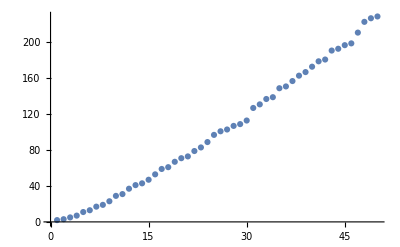

```mathematica
ListPlot[ Table[ Prime[n] ,{n, 1,50} ] ]
```

```mathematica
PrimeQ[207]
```

False

```mathematica
FactorInteger[207]
```

{{3,2},{23,1}}

## 1.2 字符串

1.字符串运算
 " StringJoin[{s1,s2,...]" | ".85将几个字符串连接在一起"
"StringLength[s]" | "给出一个串中的字符数"
"StringReverse[s]" | "颠倒串中字符的顺序"
"StringTake[s,n]" | "n>0时，由 s 的前 n 个字符形成字符串
n<0,取后面|n|个字符形成字符串"
"StringTake[s,{n}]" | "取出 s 中的第 n 个字符"
"StringTake[s,{n1,n2}]" | "取出 n1 到 n2 的字符"
"StringDrop[s,n]" | "删除前n个字符"
"StringDrop[s,{n1,n2}]" | "删除n1 到n2的字符"

```mathematica
alpha=".94ABCDEFGHIJKLMNOPQRSTUVWXYZ";
StringTake[alpha , 6]
  StringTake[alpha ,{ 6}]
  StringTake[alpha , -6] 
StringTake[alpha, {2,20,3}]
StringDrop[alpha ,{-10,-2} ]
```

.94ABCDE

E

UVWXYZ

ADGJMPS

.94ABCDEFGHIJKLMNOPZ

```mathematica
StringTake[alpha ,{2}]
```

A

```mathematica
StringTake[".94abcdefgh" , 6]
```

.94abcde

2.  插入替换字符串     "StringInsert[s,snew,n]" | " 将字符串snew插在s 中第n 个字符之前的位置"
"StringInsert[s,snew,{n1,n2,...}]" | "将字符串snew插在s中多个位置"
"StringReplacePart[s,snew,{m,n}]" | "用字符串snew替换字符串s中的第m到n个字符"
"StringReplacePart[s,snew,{{m1,n1},{m2,n2},…}]" | "用字符串snew替换字符串s中的第m1到n1,m2到n2,…等位置的字符"
"StringReplace[s,{规则}]" | " 按规则替换字符串的部分"

```mathematica
StringInsert[alpha, "**", {2, 3, -2}]
```

.94**A**BCDEFGHIJKLMNOPQRSTUVWXY**Z

```mathematica
StringReplacePart[alpha," xxx", {3, 7}]
```

.94A xxxGHIJKLMNOPQRSTUVWXYZ

```mathematica
StringReplace["The cat in the hat. ", "the" -> "a", IgnoreCase -> True]
```

a cat in a hat.

3.字符串的位置
Stringposition[s, sub]              给出 s 中子串出现的起始和结束位置的列表
Stringposition[s, sub, k]         给出 s 中子串出现的前k次位置的列表
StringCount[s, sub]                  给出 s 中子串出现的次数

```mathematica
s="They worked on the land with much difficulty and were beset by a devastating plague in which half of the Pilgrim died in the long winter of 1620. In the spring of 1621，an Indian brave named Squanto and her Wampanoag tribe came to their help.The tribe taught the Pilgrims how to work the earth and plant corn，beans，pumpkins，squash and other crops.";
StringPosition[s,"the"]
StringPosition[s,"w"]
```

{{16,18},{102,104},{122,124},{150,152},{231,233},{259,261},{284,286},{336,338}}

{{6,6},{25,25},{50,50},{88,88},{131,131},{274,274},{279,279}}

```mathematica
StringCount[s, "in"]
```

6

4.大小写转换
ToUpperCase[s]                         所有字符转为大写
ToLowercase[s]                          所有字符转为小写

## 1.3 变量

### 1. 变量名的定义规则：

(1) 以英文字母开头，后跟字母数字，希腊字母，中文词都可以做变量名，变量名中不能有空格和一些特殊字符。例如 x y 一般表示变量x, y的乘积。

(2) Mathematica系统的变量名区分大小写，A，a是不同的变量。系统内置函数一般是大写字母开头的，所以自己定义变量尽量避免使用系统已使用的字符如 D，N，E，I…

### 2. 变量赋值

```mathematica
a = b = 5
```

5

```mathematica
{x, y, z} = {1, 2, 3}
```

{1,2,3}

```mathematica
y
```

2

```mathematica
E^x
```

ⅇ

```mathematica
u = Table[i^2, {i, 5}]
```

{1,4,9,16,25}

```mathematica
u[[3]]
```

9



```mathematica
g = Plot[Sin[x], {x, 0, 2 Pi}]; Show[g]
```

对于已赋值的变量，用Unset[var] 或者 var =. 清除赋值
Clear[var] 清除变量的值和定义。以免笔记本中使用了重复变量名产生错误.

```mathematica
Clear[x,y,z];
```

```mathematica
u=.
```

```mathematica
u[[1]]
```

Part::partd: Part specification u⟦1⟧ is longer than depth of object.

u⟦1⟧

```mathematica
x = 3
x^2 + 1
E^x
x = 1 + a
x^2 + 1
```

3

10

ⅇ^3

1+a

1+(1+a)^2

变量一旦赋值，后续运算中同一变量都将代入此值运算，除非重新赋值。所以在一个笔记本中，我们需要及时清除变量，以免后面忘记而造成错误.

```mathematica
x =.
x^2 + 1
```

1+x^2

3. 要对一个特定的表达式进行局部赋值，使用 "替换算符" /., 它是由两个字符组成，中间没有空格

```mathematica
t = 1 + 2 x
```

1+2 x

```mathematica
t /. x -> 3
```

7

```mathematica
t
```

1+2 x

```mathematica
x=3
```

3

```mathematica
t
```

7

```mathematica
x=.;a=.
```

可同时替换多个变量的值，将替换规则用 {} 括起来即可.

```mathematica
(x + y) (x - y) /. {x -> 1, y -> 1 + a}
```

-a (2+a)

## 1.4 列表

列表是Mathematica中的基本对象，通常用来表示：数组 （向量）、矩阵、集合、数据库中的记录、数据结构中的树和图等。列表形式：用花括号围起来的有限个元素，元素之间用逗号分割。一个列表可以包含任意多个元素，列表中的元素可以是不同类型的任何Mathematica对象。Mathematica 列表本质上是提供一种把任何类型的表达式收集在一起的方法.

```mathematica
t={2,3,4}
t x+1
```

{2,3,4}

{1+2 x,1+3 x,1+4 x}

### 1. 列表的生成

" Range[n]" | "生成由前 n 个相邻整数组成的列表"
"Range[m,n]" | "生成由从m到 n 的相邻整数组成的列表"
"Range[m,n,d]" | "生成由从m到 n 的间隔为d的整数组成的列表"

```mathematica
Range[25,5,-2]
```

{25,23,21,19,17,15,13,11,9,7,5}

```mathematica
Range[1/3,1,1/12]
```

{1/3,5/12,1/2,7/12,2/3,3/4,5/6,11/12,1}

"Table[expr，{n}]" | "由表达式的 n 份拷贝生成的列表"
"Table[expr，{k,n}]" | " 由表达式在 k 从 1 取到 n 时的值生成成的列表"
"Table[expr，{k,m,n}]" | "由表达式在 k 从 m 取到 n 时的值生成成的列表"
"Table[expr，{k,m,n,d}] " | "由表达式在 k从 m 到 n步长为d 时的值生成列表"
"Table[expr，{i,m1,n1},{j,m2,n2}]" | " 生成嵌套的列表"

```mathematica
Table[x,10]
```

{x,x,x,x,x,x,x,x,x,x}

```mathematica
Table[x^2,{x,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[1/x,{x,3,13}]
```

{1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13}

```mathematica
Table[Sqrt[x],{x,3,13,2}]
```

{√3,√5,√7,3,√11,√13}

```mathematica
Table[i+j,{i,1,3},{j,1,5}]
```

```mathematica
{{2,3,4,5,6},{3,4,5,6,7},{4,5,6,7,8}}//MatrixForm
```

(2 | 3 | 4 | 5 | 6
3 | 4 | 5 | 6 | 7
4 | 5 | 6 | 7 | 8)

"Array[f,n]" | "由n个值f[1],f[2],…,f[n] 组成的列表"
"Array[f,n,r]" | "由f[r],f[r+1],.85,f[r+n-1] 组成的列表"
"Array[f,{m,n}]" | "由 f[i,j],i=1,.85,m,j=1,.85,n 组成"
"Array[f,{m,n},{r,s}]" | "{{f[r,s],f[r,s+1] .85f[r,s+n-1]} ...f[r+m-1,s],f[r+m-1,s+1],.85f[r+m-1,s+n-1]}} "

```mathematica
f[x_] = x^2
```

x^2

```mathematica
Array[f,3,7]
```

{49,64,81}

```mathematica
Clear[g]
```

```mathematica
g[x_,y_]=x^2+2y
Array[g,{3,5}]
Array[g,{5,3}]
Array[g,{5,3},{2,2}]
```

x^2+2 y

{{3,5,7,9,11},{6,8,10,12,14},{11,13,15,17,19}}

{{3,5,7},{6,8,10},{11,13,15},{18,20,22},{27,29,31}}

{{8,10,12},{13,15,17},{20,22,24},{29,31,33},{40,42,44}}

### 2. 列表元素提取

"First[list],Last[list]" | "返回列表的第一个 （最后一个） 元素"
"Part[list,k] 或 list[[k]]" | "返回list 中第k 个元素"
"Part[list,-k] 或 list[[-k]]" | "返回list 中倒数第k 个元素"

```mathematica
ClearAll
```

ClearAll

```mathematica
list={{a,b,c,d},{e,f,g,h},{i,j,k,l}};
```

```mathematica
list[[1]](* 第一个列表元素*)
```

{a,5,c,d}

```mathematica
list[[1,2]]
```

5

```mathematica
list[[{2,3}]]
```

{{e,f,g,h},{i,j,k,l}}

```mathematica
list[[{2,3},{1}]] (*第二，三个列表中第1个元素*)
list[[{2,3},{1,2}]]
```

{{e},{i}}

{{e,f},{i,j}}

```mathematica
b=.
```

### 3. 列表元素修改

"Rest[list]" | "去掉list第一个元素"
"Drop[list,n]" | "去掉list的前n个元素"
"Drop[list,-n]" | "去 掉 list的 后n个元素"
"Drop[list,{m,n,s}]" | "去掉list的从第m到第n个之间,步长为s的元素"
"Delete[list,i]" | "删去list的第 i个元素"
"Delete[list,{i,j,...}]" | "删去 list的第 i，j，… 个元素 "

```mathematica
Delete[{a,b,c,d},3]
```

{a,b,d}

```mathematica
Drop[{a,b,c,d},{3,3}]
```

{a,b,d}

"Prepend[list,s]" | "在 list 的开头添加元素s"
"Append[list,s]" | "在 list 的末尾添加元素 s"
"Insert[list,s,i]" | "在 list 的第i位添加元素s"
"Insert[list,s,-i]" | "在 list 的倒数第i位添加元素 s"
"Insert[list,s,{{i},{j},...}]" | "在 list 的第 i，j，… 个位置上插人 s "

```mathematica
Prepend[{a,b,c},x]
```

{x,a,b,c}

```mathematica
Append[{a,b,c},x]
```

{a,b,c,x}

```mathematica
Insert[{a,b,c},x,2]
```

{a,x,b,c}

```mathematica
Insert[{a,b,c},x,{{2},{3}}]
```

{a,x,b,x,c}

" ReplacePart[list,new,i]" | "用 new 替换list 中第i个元素"
"ReplacePart[list,new,{i,j,...}]" | "用 new 替换 list[[i,j,.85]]"
"PadLeft[list,length]" | "通过在左边填充0得到长度length的列表"
"PadLeft[list,length,x]" | "通过在左边填充x得到长度length的列表"
"PadLeft[list,length,{x1,x2,...}]" | " 通过在左边循环填充x1,x2,.85得到长度length的列表"
"Padright[list,length,.85...]" | " 在右边填充"

```mathematica
PadLeft[{a,b,c},10]
```

{0,0,0,0,0,0,0,a,b,c}

```mathematica
PadLeft[{a,b,c},10,{x,y}]
```

{x,y,x,y,x,y,x,a,b,c}

### 4. 列表元素查找

"Position[list,s]" | "s 在list 中的位置"
"Count[list,s]" | "s 作为list 的元素所给出的次数"
"MemberQ[list,s]" | "检测s 是否为 list 的元素"
"FreeQ[list,s]" | "检测 s是 否 不 在 中"

```mathematica
Position[{a,b,c,a,b},a]
```

{{1},{4}}

```mathematica
Count[{a,b,c,a,b},a]
```

2

```mathematica
MemberQ[{a,b,c},d]
```

False

### 5. 列表组合与拆分

"Join[list1,list2,.85...]" | "把列表连接在一起"
"Union[list1,list2,.85...]" | "列表的并 (合并列表，删除重复的元素)"
"Intersection[list1,list2,.85...]" | "给出listi中共有的元素的列表"
"Complement[s,list1,list2,....85]" | "给出在s 中，但不在listi中的兀素的列表"

```mathematica
Join[{c,a,b},{d,a,c},{a,e}]
```

{c,a,b,d,a,c,a,e}

```mathematica
Union[{c,a,b},{d,a,c},{a,e}]
```

{a,b,c,d,e}

```mathematica
Intersection[{c,a,b},{d,a,c},{a,e}]
```

{a}

```mathematica
Complement[{c,a,b},{d,a,c},{a,e}]
```

{b}

"Partition[list,n]" | "把列表分成n 个元素一组"
"Partition[list,n,d]" | "使用偏移 d 进行逐次分组"
"Partition[list,{n1,n2,...}]" | "把嵌套列表拆分成{n1,n2,…}大小的子块"
"Split[list]" | "把list按邻接的相同元素进行分组 "

```mathematica
t={a,b,c,d,e,f,g}
Partition[t,2]
```

{a,b,c,d,e,f,g}

{{a,b},{c,d},{e,f}}

```mathematica
Partition[t,3,1]
```

{{a,b,c},{b,c,d},{c,d,e},{d,e,f},{e,f,g}}

```mathematica
Split[{a,a,b,b,b,a,a,a,b}]
```

{{a,a},{b,b,b},{a,a,a},{b}}

### 6. 重排列表

"Sort[list]" | "把列表元素整理成标准顺序"
"Reverse[list]" | "对 list 的元素进行反向排序"
"RotateLeft[list,n]" | "把列表元素向左轮换 n 个位置"
"RotateRight[list,n]" | "把列表元素向右轮换 n 个位置"

```mathematica
Sort[{b,c,c,a,b,a}]
```

{a,a,b,b,c,c}

```mathematica
Reverse[{9,3,1,42,71,67,15}]
```

{15,67,71,42,1,3,9}

```mathematica
RotateLeft[{9,3,1,42,71,67,15},3]
```

{42,71,67,15,9,3,1}

#### 嵌套列表的重排

"Transpose[list]" | "交换列表的前两层"
"Flatten[list]" | "压平list的所有层"
"Flatten[list,n]" | "压平 list 的前n层"
"FlattenAt[list,i]" | "压平位置i处的子列表"

```mathematica
A={{1,2,3},{4,5,6},{7,8,9}}
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
Transpose[A]
```

{{1,4,7},{2,5,8},{3,6,9}}

```mathematica
Flatten[A]
```

{1,2,3,4,5,6,7,8,9}

## 1.5 表达式

多种不同形式的运算对象:  数学公式、列表、字符串、图形等 都可以称为表达式.
典型例子是f[x,y]， 不需要经常将表示式写为f[x,y,…]的形式，
 例如:x+y 也是一个表达式.当输入 x+ y 时， Mathematica 将它转换成标准形式 Plus[x，y] .
 当输出时， Mathematica 仍然给出 x + y.
  对 +，-，*，/ ^ 等运算也是一样的.事实上， 对任何输入， Mathematica 总是把它当作表达式处理.

```mathematica
FullForm[x^n]
```

Power[x,n]

```mathematica
FullForm[{a,b,c}]
```

List[a,b,c]

```mathematica
FullForm[a=b]
```

b

```mathematica
FullForm[a x^2+(y+z)^2+E^x]
```

Plus[Power[E,x],Times[b,Power[x,2]],Power[Plus[y,z],2]]

对象f是表达式f[x,y,￿]的头.可以用Head[expr] 去分离此表达式的头部， 特别当用 Mathematica 编程时， 经常要测试一个表达式的头以确定这个表达式是什么.

```mathematica
Head[(y+z)^2]
```

Power

```mathematica
Head[23432]
```

Integer

### 1. 表达式的特殊输入方式：

Mathematica 语言有确定的语法规则， 按照这些规则将你的输入转化为内部格式。
（1）	将单个输入进行分组  例如 a+x2^b+x^2 先算指数运算， 再算加法， x1被理解成1个变量而不是 x* 2^b, 具有较高优先级的变量比优先级低的变量先进行分组.

（2）	表达式4种输入方式

f[x,y] | f[x,y] 标准形式
f@x | f[x] 的前缀格式
x//f | f[x] 的后缀格式
x~f~y | f[x,y] 的嵌入格式

```mathematica
x+y//f
```

(x+y)^2

```mathematica
3/7+Pi//N
```

3.57016

```mathematica
{a,b,c}~Join~{1,2,3}
```

{b,b,c,1,2,3}

// f    放在任何表达式末尾时， 则f是相对整个表达式的， f@x 的优先级更高，

```mathematica
f@x+y 
 f@(x+y)
```

x^2+y

(x+y)^2

### 2. 算术表达式

算术运算的优先级遵从数学习惯，同级运算符按照从左到右的顺序，赋值则按照从右到左的顺序.
Mathematica提供了两种类型的赋值
（1）lhs = rhs 是一个即时赋值语句，这里在进行赋值时，就对 rhs 进行计算
（2）lhs:=rhs 是一个延时赋值语句,以后每次调用时才计算 rhs
例如 定义

```mathematica
f[1]=Sqrt[2];
f[n_]:=Sqrt[2+f[n-1]];
f[10]
```

√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√2)))))))))

有时候， 想计算表达式的值， 而又不想给某个符号賦值， 那么可以用替换符号/.
例如： 计算 x^2+2x+5在 x=3的值，但不想将x赋值为3.

```mathematica
x^2+2 x+5/.x->3
```

20

### 3. 逻辑表达式

取值为True， False的表达式称为逻辑表达式。

(1) Equal[x, y] 或 x == y 的值为True当且仅当 x 与 y 有相同的值

(2) Unequal[x,y] 或 x!=y  的值为真当且仅当 x 与 y的值不同

(3) Less[x,y] 或 x <y 的值为真当且仪当在数值上 x 小于 y

(4) Greater[x, y] 或 x >y 的值为真当且仅当在数值上 x 大于 y

(5) LessEqual[x, y] 或 x<= y 的值为真当且仅当在数值上 x 小于或等于y

(6) GreaterEqual[x,y] 或 x>=y 的值为真当且仅当在数值上 x 大于或等于y

逻辑操作：p,q是逻辑表达式
And[p,q], p&&q | p与q的值都为 True 时，它的值为 True
Or[p,q],p||q | p或q的值(或两者同时)为True 时,它的值为 True
Xor[p,q] | p或q的值仅有一个为True 时,它的值为 True
Not[p], !p | p的值为False时，它的值为True
 Implies[p,q], p=>q | 如果p为True，q为False，它的值为True
Equivalent[p,q] | Or[And[p,q],Nor[p,q]]

```mathematica
Solve[x+2y==1&&3x+y==2,{x,y}]
```

{{x→3/5,y→1/5}}